```mathematica
NS["fmri_alzheimer170317.nb"]
```

```mathematica
(* Load data given by Claudia *)
(*relevant={7,3,27,28,2,10,16,22,4,12,18,24};*)
(*relevant=Range[28];*)
(* relevant quantities found in fmri_alzheimer_reduction170317.nb *)
relevant={1,2,3,8,9,12,15,16,20,21,23,24};
datah=Import["claudia_RGS_graphprop22_Con.txt","CSV"];
datah=datah[[relevant,2;;]];

smean=Mean[T@datah];snorm=1/Std[T@datah];
datah=N[snorm*(datah-smean)];

dataa=Import["claudia_RGS_graphprop22_AD.txt","CSV"];
quantities=T[dataa][[1]][[relevant]];
dataa=dataa[[relevant,2;;]];
dataa=N[snorm*(dataa-smean)];

datam=Import["claudia_RGS_graphprop22_MCI.txt","CSV"];
datam=datam[[relevant,2;;]];
datam=N[snorm*(datam-smean)];

nq=Length[quantities];
health={1,2,3};
data[1]=datah;data[2]=dataa;data[3]=datam;
```

```mathematica
Do[nindiv[i]=Length[T[data[i]]];
means[i]=Mean@T@data[i];
dscatter[i]=(nindiv[i]+1)/nindiv[i]*(data[i]-means[i]).T[data[i]-means[i]]; 
idscatter[i]=Inverse[dscatter[i]];
scalematrix[i]=dscatter[i]/(nindiv[i]+1-nq);
iscalematrix[i]=Inverse[scalematrix[i]];
param[i]=nindiv[i]+1-nq;
,{i,health}];
```

```mathematica
lnpdf[i_,x_]:=Log@PDF[MultivariateTDistribution[means[i],scalematrix[i],param[i]],x]
```

```mathematica
Sort@quantities
```

{closeness centrality3,cluster coeff1.,cluster coeff.4,graphweights1,graphweights2,graphweights3,graphweights4,modularity,shortest path1,shortest path3,weighted degree2,weighted degree4}

```mathematica
Dimensions/@{datah,dataa,datam}
```

{{12,26},{12,14},{12,16}}

```mathematica
Table[{i,quantities[[i]]},{i,nq}]//MF
```

(1 | graphweights1
2 | shortest path1
3 | cluster coeff1.
4 | modularity
5 | graphweights2
6 | weighted degree2
7 | graphweights3
8 | shortest path3
9 | closeness centrality3
10 | graphweights4
11 | cluster coeff.4
12 | weighted degree4)

```mathematica
(* used mathematica's built-in distribution *)
lnpdfold[i_,x_]:=Log[Gamma[(nindiv[i]+1)/2]]-Log[Gamma[(nindiv[i]+1-nq)/2]]-Log[Det[dscatter[i]*Pi]]/2-(nindiv[i]+1)*Log[1+(x-means[i]).idscatter[i].(x-means[i])]/2;
```

```mathematica
plevel[i_,p_]:=InverseCDF[FRatioDistribution[nq,param[i]],p]
```

```mathematica
plevel[2,0.95]
```

8.74464

```mathematica
Do[es=Eigensystem[scalematrix[i]*param[i]];eva[i]=es[[1]];eve[i]=Last[es[[2]]];,{i,3}]
```

```mathematica
Table[eva[i],{i,3}]//MF
```

(174.395 | 77.7677 | 28.4726 | 17.4952 | 12.8357 | 6.81227 | 3.03175 | 1.73433 | 0.894374 | 0.37008 | 0.114628 | 0.076559
3903.34 | 44.7336 | 24.1576 | 5.36985 | 0.982701 | 0.195629 | 0.0638555 | 0.0142447 | 0.00948675 | 0.0041682 | 0.00149723 | 5.33527×10^-6
169.48 | 41.025 | 10.9821 | 3.36219 | 1.18148 | 0.792785 | 0.323813 | 0.185976 | 0.0688527 | 0.0395949 | 0.00185752 | 0.000120496)

```mathematica
Table[eve[i],{i,3}]//T//MF
```

(0.533413 | 0.00932564 | 0.0781962
-0.209922 | 0.000854921 | -0.00151329
-0.519453 | 0.0297116 | -0.0455079
0.00980465 | 0.00254263 | -0.00142218
-0.487661 | -0.051848 | -0.013942
0.060103 | -0.0697706 | -0.31805
-0.19059 | 0.062851 | 0.0669002
0.0675029 | -0.00107871 | -0.00298366
0.0631045 | -0.00051902 | 0.0818599
0.337999 | -0.17334 | -0.0740643
0.0125661 | 0.00975543 | 0.0463802
0.028018 | 0.978455 | 0.933615)

```mathematica
xx=Array[x,nq]
```

{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12]}

```mathematica
{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12]}
```

{x[1],x[2],x[3],x[4],x[5],x[6],x[7],x[8],x[9],x[10],x[11],x[12]}

```mathematica
region=FS[Norm[xx]<100]
```

√(Abs[x[1]]^2+Abs[x[2]]^2+Abs[x[3]]^2+Abs[x[4]]^2+Abs[x[5]]^2+Abs[x[6]]^2+Abs[x[7]]^2+Abs[x[8]]^2+Abs[x[9]]^2+Abs[x[10]]^2+Abs[x[11]]^2+Abs[x[12]]^2)<100

```mathematica
fun=FS@Sum[lnpdf[i,xx],{i,3}];
```

```mathematica
maxp=FindMaximum[{fun,region},xx]
```

{16.7611,{x[1]→-0.59086,x[2]→0.66996,x[3]→-0.55793,x[4]→0.435517,x[5]→-0.700426,x[6]→-0.402819,x[7]→-0.349592,x[8]→0.0903144,x[9]→-0.57563,x[10]→-0.538019,x[11]→-0.425067,x[12]→-0.230233}}

```mathematica
NMaximize[{fun,region},xx]
```

{16.7611,{x[1]→-0.591019,x[2]→0.670293,x[3]→-0.558093,x[4]→0.435883,x[5]→-0.700536,x[6]→-0.402883,x[7]→-0.349666,x[8]→0.0904953,x[9]→-0.575679,x[10]→-0.538082,x[11]→-0.425073,x[12]→-0.230245}}

```mathematica
maxpoint=(xx/.maxp[[2]])
```

{-0.59086,0.66996,-0.55793,0.435517,-0.700426,-0.402819,-0.349592,0.0903144,-0.57563,-0.538019,-0.425067,-0.230233}

```mathematica
region=FS[Norm[xx]<100]
```

√(Abs[x[1]]^2+Abs[x[2]]^2+Abs[x[3]]^2+Abs[x[4]]^2+Abs[x[5]]^2+Abs[x[6]]^2+Abs[x[7]]^2+Abs[x[8]]^2+Abs[x[9]]^2+Abs[x[10]]^2+Abs[x[11]]^2+Abs[x[12]]^2)<100

```mathematica
fun=Simplify@Sum[lnpdf[i,xx],{i,2}];
```

```mathematica
maxp=FindMaximum[{fun,region},xx]
```

{9.2122,{x[1]→-0.541207,x[2]→0.548849,x[3]→-0.498916,x[4]→0.333813,x[5]→-0.626627,x[6]→-0.291671,x[7]→-0.258092,x[8]→0.00476958,x[9]→-0.547147,x[10]→-0.474993,x[11]→-0.445558,x[12]→-0.214895}}

```mathematica
NMaximize[{fun,region},xx]
```

{9.2122,{x[1]→-0.541134,x[2]→0.548537,x[3]→-0.498828,x[4]→0.334788,x[5]→-0.626376,x[6]→-0.291485,x[7]→-0.257743,x[8]→0.00445927,x[9]→-0.546636,x[10]→-0.474765,x[11]→-0.444998,x[12]→-0.214862}}

```mathematica
maxpointha=(xx/.maxp[[2]])
```

{-0.541207,0.548849,-0.498916,0.333813,-0.626627,-0.291671,-0.258092,0.00476958,-0.547147,-0.474993,-0.445558,-0.214895}

```mathematica
fun=Simplify@Sum[lnpdf[i,xx],{i,{2,3}}];
```

```mathematica
maxp=FindMaximum[{fun,region},xx]
```

{18.6267,{x[1]→-0.703135,x[2]→0.935819,x[3]→-0.674431,x[4]→0.445894,x[5]→-0.800518,x[6]→-0.461356,x[7]→-0.445203,x[8]→0.209234,x[9]→-0.622608,x[10]→-0.605914,x[11]→-0.432148,x[12]→-0.241078}}

```mathematica
NMaximize[{fun,region},xx]
```

{18.6267,{x[1]→-0.702106,x[2]→0.933743,x[3]→-0.673417,x[4]→0.441836,x[5]→-0.800143,x[6]→-0.461192,x[7]→-0.44522,x[8]→0.208088,x[9]→-0.62258,x[10]→-0.605804,x[11]→-0.432235,x[12]→-0.241054}}

```mathematica
maxpointam=(xx/.maxp[[2]])
```

{-0.703135,0.935819,-0.674431,0.445894,-0.800518,-0.461356,-0.445203,0.209234,-0.622608,-0.605914,-0.432148,-0.241078}

```mathematica
fun=Simplify@Sum[lnpdf[i,xx],{i,{1,3}}];
```

```mathematica
maxp=FindMaximum[{fun,region},xx]
```

{6.7877,{x[1]→-0.346791,x[2]→0.363003,x[3]→-0.352931,x[4]→0.325477,x[5]→-0.421659,x[6]→-0.249764,x[7]→-0.178621,x[8]→0.0232986,x[9]→-0.521179,x[10]→-0.307931,x[11]→-0.365065,x[12]→-0.186661}}

```mathematica
NMaximize[{fun,region},xx]
```

{18.6267,{x[1]→-0.702106,x[2]→0.933743,x[3]→-0.673417,x[4]→0.441836,x[5]→-0.800143,x[6]→-0.461192,x[7]→-0.44522,x[8]→0.208088,x[9]→-0.62258,x[10]→-0.605804,x[11]→-0.432235,x[12]→-0.241054}}

```mathematica
maxpointhm=(xx/.maxp[[2]])
```

{-0.346791,0.363003,-0.352931,0.325477,-0.421659,-0.249764,-0.178621,0.0232986,-0.521179,-0.307931,-0.365065,-0.186661}

```mathematica
(* The three distributions are 6-dimensional. To visualize them, in this 6D space we choose a 2D section that passes through their centres. Then we plot the curves of 1 and 2 standard deviations. *)
point[1]=maxpointha;point[2]=maxpointhm;point[3]=maxpointam;

(* Affine-combination coefficients for the contour plot *)
ac[1,x_,y_]=-x-y/Sqrt[3]+1;ac[3,x_,y_]=x-y/Sqrt[3];ac[2,x_,y_]=Simplify[1-ac[1,x,y]-ac[3,x,y]];
seq=FS@Table[Sum[ac[ii,x,y]*point[ii][[jj]],{ii,3}],{jj,nq}]
```

{-0.541207-0.161928 x+0.317981 y,0.548849+0.38697 x-0.438014 y,-0.498916-0.175515 x+0.269902 y,0.333813+0.112081 x-0.0743355 y,-0.626627-0.173892 x+0.337073 y,-0.291671-0.169685 x+0.146358 y,-0.258092-0.187111 x+0.199794 y,0.00476958+0.204464 x-0.0966521 y,-0.547147-0.0754611 x+0.073553 y,-0.474993-0.130921 x+0.268494 y,-0.445558+0.0134095 x+0.0852034 y,-0.214895-0.0261823 x+0.0477191 y}

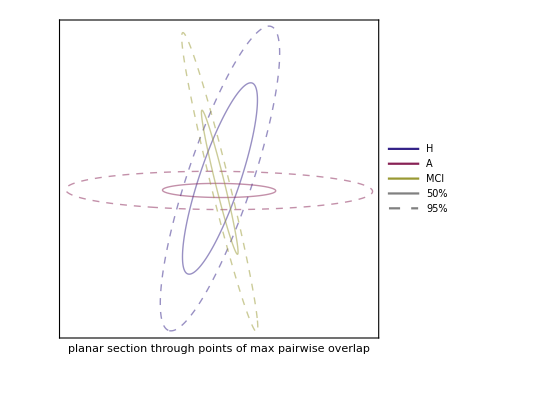

```mathematica
(* We plot the three separately and then join them *)
myfontsize=21;
colours={blue,red,yellow};Do[cont[i]=ContourPlot[(seq-means[i]).iscalematrix[i].(seq-means[i]),{x,-35,35},{y,-35,35},Contours->{plevel[i,0.5]*nq,plevel[i,0.95]*nq},ContourShading->None,ContourStyle->{Directive[Opacity[0.5],Thick,colours[[i]]],Directive[Dashed,Opacity[0.5],Thick,colours[[i]]]},PlotPoints->300,FrameTicks->None,FrameLabel->Evaluate[myaxes[{"planar section through points of max pairwise overlap",""}]],PlotLegends->If[i==3,mylegendsc[{blue,red,yellow,White,{Gray,Thick},{Gray,Dashed,Thick}},{"H","A","MCI"," ", "50%","95%"}],None],(*PlotLabel->mylabels[{"1 and 2 standard deviations"}],*)PlotRange->All],{i,{1,3,2}}];
centres=Graphics[{{red,PointSize[Large],Point[{0,0}]}(*,{red,PointSize[Large],Point[{1/2,Sqrt[3]/2}]}*)(*,{yellow,PointSize[Large],Point[{1,0}]}*)}];

Show[Join[Array[cont,3](*,{centres}*)]]
```

```mathematica
expdf["std95_12_params_pairwiseoverlaps"]
```

../work/std95_12_params_pairwiseoverlaps.pdf

```mathematica
(* The three distributions are 6-dimensional. To visualize them, in this 6D space we choose a 2D section that passes through their centres. Then we plot the curves of 1 and 2 standard deviations. *)
point[1]=means[1];point[2]=means[2];point[3]=means[3];

(* Affine-combination coefficients for the contour plot *)
ac[1,x_,y_]=-x-y/Sqrt[3]+1;ac[3,x_,y_]=x-y/Sqrt[3];ac[2,x_,y_]=Simplify[1-ac[1,x,y]-ac[3,x,y]];
seq=FS@Table[Sum[ac[ii,x,y]*point[ii][[jj]],{ii,3}],{jj,nq}]
```

{-4.27009×10^-17-0.30036 x-0.517448 y,6.93889×10^-16+0.422756 x+0.921967 y,7.62211×10^-16-0.31284 x-0.391014 y,6.12758×10^-16+0.493798 x+0.247622 y,-1.57993×10^-16-0.278029 x-0.369567 y,-4.27009×10^-18-0.25148 x-0.154525 y,-9.39419×10^-17+0.0245361 x-0.139253 y,-7.25915×10^-17+0.0698809 x+0.367994 y,1.06752×10^-16-0.379939 x+2.51088 y,4.27009×10^-17-0.00032102 x-0.242388 y,2.77556×10^-17-0.322087 x+3.92 y,2.13504×10^-18-0.191212 x-0.122483 y}

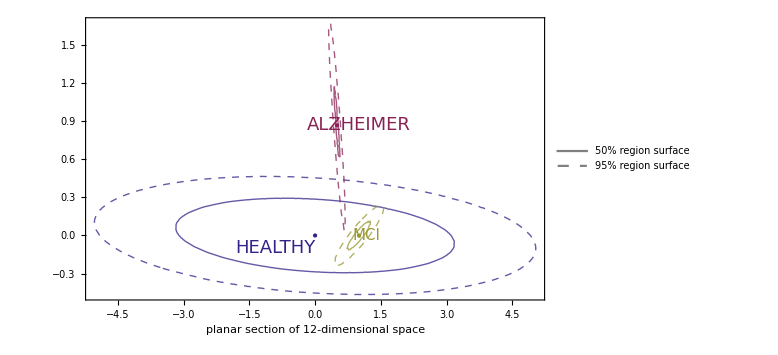

```mathematica
(* We plot the three separately and then join them *)
myfontsize=24;
colours={blue,red,yellow};Do[cont[i]=ContourPlot[(seq-means[i]).iscalematrix[i].(seq-means[i]),{x,-35,35},{y,-35,35},Contours->{plevel[i,0.5]*nq,plevel[i,0.95]*nq},ContourShading->None,ContourStyle->{Directive[Opacity[0.75],Thick,colours[[i]]],Directive[Dashed,Opacity[0.75],Thick,colours[[i]]]},PlotPoints->200,FrameTicks->Auto,Evaluate@myframestyle,AspectRatio->1/GoldenRatio,FrameLabel->Evaluate[myaxes[{"planar section of 12-dimensional space",""}]],PlotLegends->If[i==3,mylegendsc[{(*blue,red,yellow,White,*){Gray,Thick},{Gray,Dashed,Thick}},{(*"H","A","MCI"," ", *)"50% region surface","95% region surface"}],None],(*PlotLabel->mylabels[{"1 and 2 standard deviations"}],*)PlotRange->All],{i,{1,3,2}}];
centres=Graphics[{{blue,PointSize[Large],Point[{0,0}]},{red,PointSize[Large],Point[{1/2,Sqrt[3]/2}]},{yellow,PointSize[Large],Point[{1,0}]}}];texts=Graphics[{Text[Style["HEALTHY",blue,18,Thickness[1/50],FontFamily->"Palatino"],{0,-0.1},{0.8,0},{1,-0.1}],Text[Style["ALZHEIMER",red,18,Thickness[1/50],FontFamily->"Palatino"],{1/2+0.5,Sqrt[3]/2},{0,0},{0.07,-1}],Text[Style["MCI",yellow,15,Thickness[1/50],FontFamily->"Palatino"],{1+0.5,0},{0.5,0},{0.6,1}]}];

show[Join[Array[cont,3],{centres},{texts}]]
```

```mathematica
expdf["std95_12_params_centres"]
```

../work/std95_12_params_centres.pdf

```mathematica
(* The three distributions are 6-dimensional. To visualize them, in this 6D space we choose a 2D section that passes through their centres. Then we plot the curves of 1 and 2 standard deviations. *)
point[1]=maxpointha;point[2]=maxpointhm;point[3]=maxpointam;
(*point[1]=means[1];point[2]=means[2];point[3]=means[3];*)

(* Affine-combination coefficients for the contour plot *)
ac[1,x_,y_]=-x-y/Sqrt[3]+1;ac[3,x_,y_]=x-y/Sqrt[3];ac[2,x_,y_]=Simplify[1-ac[1,x,y]-ac[3,x,y]];
seq=FS@Table[Sum[ac[ii,x,y]*point[ii][[jj]],{ii,3}],{jj,nq}]
```

{-0.541207-0.161928 x+0.317981 y,0.548849+0.38697 x-0.438014 y,-0.498916-0.175515 x+0.269902 y,0.333813+0.112081 x-0.0743355 y,-0.626627-0.173892 x+0.337073 y,-0.291671-0.169685 x+0.146358 y,-0.258092-0.187111 x+0.199794 y,0.00476958+0.204464 x-0.0966521 y,-0.547147-0.0754611 x+0.073553 y,-0.474993-0.130921 x+0.268494 y,-0.445558+0.0134095 x+0.0852034 y,-0.214895-0.0261823 x+0.0477191 y}

```mathematica
entropy[x_,y_]=-(Sum[Exp[lnpdf[i,seq]]*lnpdf[i,seq],{i,3}]/Sum[Exp@lnpdf[i,seq],{i,3}]-Log[Sum[Exp@lnpdf[i,seq],{i,3}]])/Log[3];
```

```mathematica
entropy[0,0]
```

5.63017×10^-15

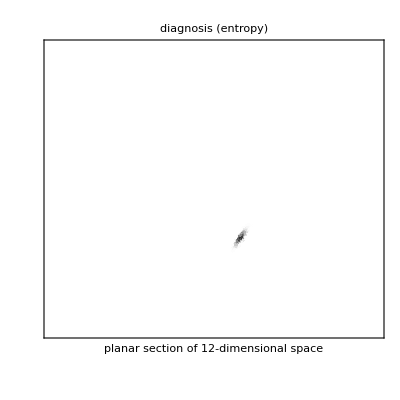

```mathematica
myfontsize=15;labels=Directive[Black,15,Thickness[1/500],FontFamily->"Palatino"];
colours={blue,red,yellow};dplot=DensityPlot[entropy[x,y],{x,-6,6},{y,-1,2},ColorFunction->(GrayLevel[1-#]&),PlotPoints->60,FrameTicks->None,Evaluate@myframestyle,AspectRatio->1,PlotLabel->Column[{Style["diagnosis (entropy)",Black,18,Thickness[1/50],FontFamily->"Palatino"],Evaluate@BarLegend[{(GrayLevel[1-#]&),{0,1}},LabelStyle->Evaluate@labels,LegendLayout->"Row",TickLengths->10,FrameStyle->{{Thick,Thick},{Thin,Thin}},Ticks->{{0,"100% correct"},{1,"33% correct (chance level)"}},LegendMarkerSize->375]},Center],FrameLabel->Evaluate[myaxes[{"planar section of 12-dimensional space",""}]],(*PlotLegends->Placed[BarLegend[{(GrayLevel[1-#]&),{0,1}},LegendLayout->"Row",LabelStyle->labels,Ticks->{{0,"perfect discrimination"},{1,"complete ignorance"}},LegendMarkerSize->500],Bottom],*)(*mylegendsc[{blue,red,yellow,White,{Gray,Thick},{Gray,Dashed,Thick}},{"H","A","MCI"," ", "50%","95%"}]*)(*PlotLabel->mylabels[{"1 and 2 standard deviations"}],*)PlotRange->All]
```

```mathematica
expdfr["entropy_12_params_overlaps2"]
```

../work/entropy_12_params_overlaps2.pdf

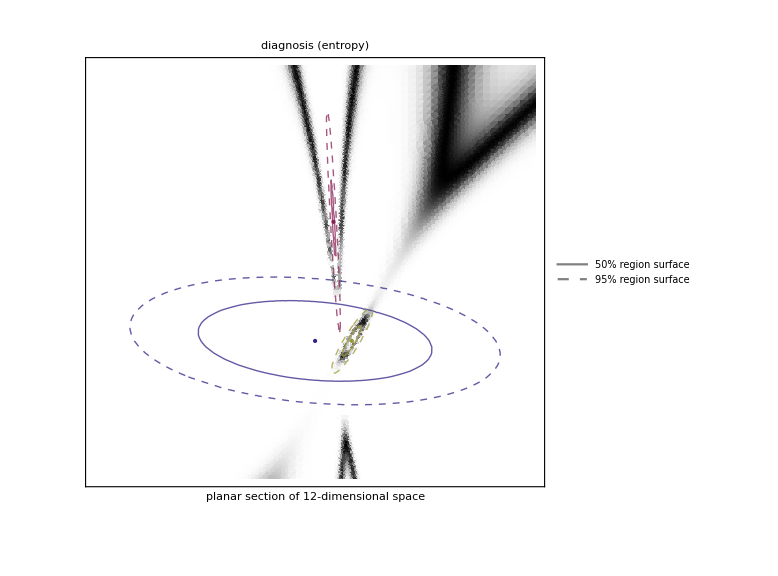

```mathematica
show[{dplot,cont[1],cont[2],cont[3],centres}]
```

```mathematica
expdfr["entropy_contours_12_params_centres"]
```

../work/entropy_contours_12_params_centres.pdf

```mathematica
(* OTHER PLANAR SECTIONS *)
```

```mathematica
centreall=Sum[means[i],{i,3}]/3;
```

```mathematica
{dir[1]=RandomReal[{0,1},12],dir[2]=RandomReal[{0,1},12]}
```

{{0.42117,0.244809,0.817044,0.986425,0.113864,0.160957,0.343207,0.00781063,0.935039,0.665205,0.677801,0.721053},{0.00947231,0.944642,0.177438,0.958039,0.605366,0.887488,0.754762,0.474247,0.931323,0.796961,0.31512,0.822823}}

```mathematica
Do[mindir[j]=+Infinity;Do[mindir[j]=Min[mindir[j],Min[Solve[(means[i]+xxx*dir[j]-means[i]).iscalematrix[i].(means[i]+xxx*dir[j]-means[i])==plevel[i,0.95]*nq,xxx,Reals][[;;,1,2]]]],{i,3}];
maxdir[j]=-Infinity;
Do[maxdir[j]=Max[maxdir[j],Max[Solve[(means[i]+xxx*dir[j]-means[i]).iscalematrix[i].(means[i]+xxx*dir[j]-means[i])==plevel[i,0.95]*nq,xxx,Reals][[;;,1,2]]]],{i,3}];
,{j,2}]
```

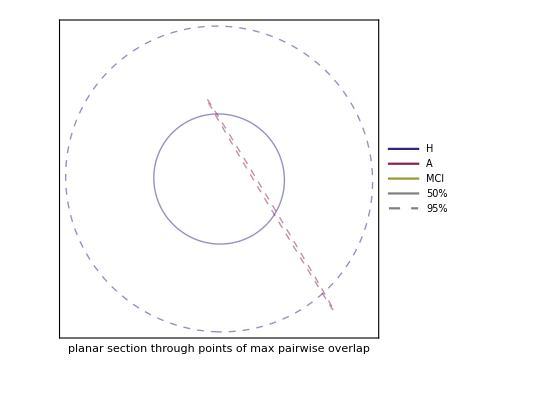

```mathematica
(* We plot the three separately and then join them *)
centreall=Sum[means[i],{i,3}]/3;
seqc=centreall+dir[1]*x+dir[2]*y;

myfontsize=21;
colours={blue,red,yellow};Do[cont[i]=ContourPlot[(seqc-means[i]).iscalematrix[i].(seqc-means[i]),{x,2*mindir[1],2*maxdir[1]},{y,2*mindir[2],2*maxdir[2]},Contours->{plevel[i,0.5]*nq,plevel[i,0.95]*nq},ContourShading->None,ContourStyle->{Directive[Opacity[0.5],Thick,colours[[i]]],Directive[Dashed,Opacity[0.5],Thick,colours[[i]]]},PlotPoints->100,FrameTicks->None,FrameLabel->Evaluate[myaxes[{"planar section through points of max pairwise overlap",""}]],PlotLegends->If[i==3,mylegendsc[{blue,red,yellow,White,{Gray,Thick},{Gray,Dashed,Thick}},{"H","A","MCI"," ", "50%","95%"}],None],(*PlotLabel->mylabels[{"1 and 2 standard deviations"}],*)PlotRange->All],{i,{1,3,2}}];
(*centres=Graphics[{{red,PointSize[Large],Point[{0,0}]}(*,{red,PointSize[Large],Point[{1/2,Sqrt[3]/2}]}*)(*,{yellow,PointSize[Large],Point[{1,0}]}*)}];*)

Show[Join[Array[cont,3](*,{centres}*)]]
```

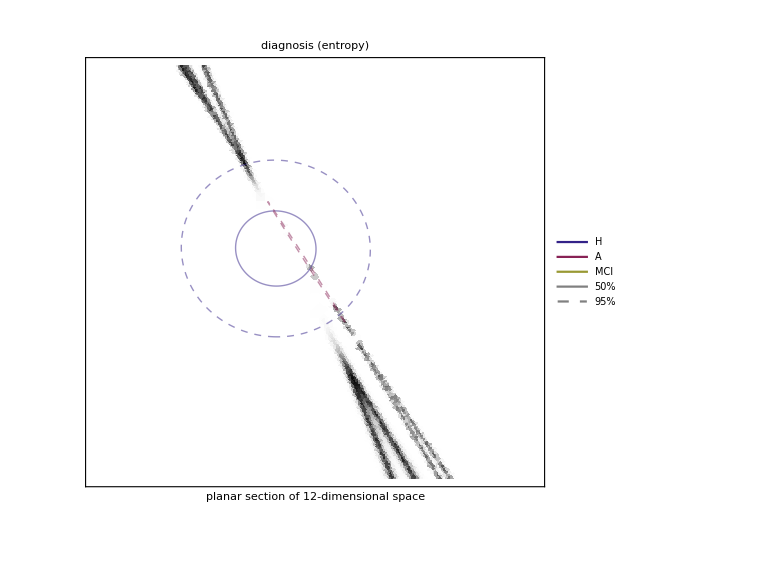

```mathematica
entropy[x_,y_]=-(Sum[Exp[lnpdf[i,seqc]]*lnpdf[i,seqc],{i,3}]/Sum[Exp@lnpdf[i,seqc],{i,3}]-Log[Sum[Exp@lnpdf[i,seqc],{i,3}]])/Log[3];

myfontsize=15;labels=Directive[Black,15,Thickness[1/500],FontFamily->"Palatino"];
colours={blue,red,yellow};dplot=DensityPlot[entropy[x,y],{x,2*mindir[1],2*maxdir[1]},{y,2*mindir[2],2*maxdir[2]},ColorFunction->(GrayLevel[1-#]&),PlotPoints->50,FrameTicks->None,Evaluate@myframestyle,AspectRatio->1,PlotLabel->Column[{Style["diagnosis (entropy)",Black,18,Thickness[1/50],FontFamily->"Palatino"],Evaluate@BarLegend[{(GrayLevel[1-#]&),{0,1}},LabelStyle->Evaluate@labels,LegendLayout->"Row",TickLengths->10,FrameStyle->{{Thick,Thick},{Thin,Thin}},Ticks->{{0,"100% correct"},{1,"33% correct (chance level)"}},LegendMarkerSize->375]},Center],FrameLabel->Evaluate[myaxes[{"planar section of 12-dimensional space",""}]],(*PlotLegends->Placed[BarLegend[{(GrayLevel[1-#]&),{0,1}},LegendLayout->"Row",LabelStyle->labels,Ticks->{{0,"perfect discrimination"},{1,"complete ignorance"}},LegendMarkerSize->500],Bottom],*)(*mylegendsc[{blue,red,yellow,White,{Gray,Thick},{Gray,Dashed,Thick}},{"H","A","MCI"," ", "50%","95%"}]*)(*PlotLabel->mylabels[{"1 and 2 standard deviations"}],*)PlotRange->All];

show[{dplot,cont[1],cont[2],cont[3]}]
```

```mathematica
expdfr["2Dsection_"<>isodate]
```

../work/2Dsection_170320T2229.pdf

```mathematica
Exp@lnpdf[1,seqf[-30,-30]]
```

4.52953×10^-16

```mathematica
Blend[{blue,red,yellow},Evaluate@{Exp@lnpdf[1,seqf[30,30]],Exp@lnpdf[2,seqf[30,30]],Exp@lnpdf[3,seqf[30,30]]}]
```

RGBColor[0.20000000000955948, 0.13333333333334596, 0.5333333333275951]

```mathematica
Blend[{blue,red,yellow},{2,1,1}]
```

RGBColor[Rational[23, 60], Rational[1, 4], Rational[2, 5]]

```mathematica
seqf[0,0]
```

{-0.541207,0.548849,-0.498916,0.333813,-0.626627,-0.291671,-0.258092,0.00476958,-0.547147,-0.474993,-0.445558,-0.214895}

```mathematica
(* These are some scripts just to copy the data on the latex file *)Grid[Table[{"$"<>ToString[i+13*2]<>"$ & C & $("<>ToString[T[datafull[[2]]][[i]]]<>")$ \\\\"},{i,12} ]]
```

$27$ & C & $({0.575399, 1.84898, 0.596428, 140.973, 0.080927, 246})$ \\
$28$ & C & $({0.687646, 1.48628, 0.691763, 144.406, 0.04448, 211})$ \\
$29$ & C & $({0.576417, 1.81166, 0.583679, 129.694, 0.051219, 226})$ \\
$30$ & C & $({0.669721, 1.5166, 0.672916, 129.926, 0.032039, 195})$ \\
$31$ & C & $({0.736418, 1.36799, 0.73886, 145.074, 0.022411, 198})$ \\
$32$ & C & $({0.743739, 1.35582, 0.746371, 174.035, 0.024474, 235})$ \\
$33$ & C & $({0.664138, 1.55512, 0.673374, 156.736, 0.034872, 237})$ \\
$34$ & C & $({0.614609, 1.69503, 0.624112, 132.756, 0.045331, 217})$ \\
$35$ & C & $({0.439049, 2.31677, 0.478943, 131.715, 0.13096, 301})$ \\
$36$ & C & $({0.728062, 1.38382, 0.730246, 165.998, 0.021884, 229})$ \\
$37$ & C & $({0.719449, 1.4011, 0.721807, 161.157, 0.020809, 225})$ \\
$38$ & C & $({0.689622, 1.49152, 0.697921, 162.061, 0.044468, 236})$ \\

```mathematica
Table[If[i<=j,ToString[(datafull[[1]].T@datafull[[1]])[[i,j]]/Length[T@datafull[[1]]]],""],{i,6},{j,6}]//MF
```

(0.402114 | 1.03346 | 0.409205 | 100.371 | 0.0324141 | 156.968
 | 2.93548 | 1.05846 | 256.904 | 0.103465 | 420.29
 |  | 0.416651 | 102.093 | 0.0335846 | 160.097
 |  |  | 25222.8 | 7.99839 | 39366.2
 |  |  |  | 0.00433914 | 13.8298
 |  |  |  |  | 62677.3)

```mathematica
hh=2;Grid[
Table[
If[i≤j,ToString[(datafull[[hh]].T@datafull[[hh]])[[i,j]]/Length@T[datafull[[hh]]]],""]<>If[j<6," & "," \\\\"],{i,6},{j,6}]]
```

0.434586 &  | 1.0248 &  | 0.439879 &  | 97.5448 &  | 0.0277439 &  | 148.531 \\
 &  | 2.6401 &  | 1.04242 &  | 234.405 &  | 0.0817666 &  | 373.415 \\
 &  |  &  | 0.44537 &  | 98.8598 &  | 0.0284874 &  | 150.919 \\
 &  |  &  |  &  | 22091. &  | 6.58946 &  | 33961.6 \\
 &  |  &  |  &  |  &  | 0.00304913 &  | 11.2511 \\
 &  |  &  |  &  |  &  |  &  | 53432.3 \\

```mathematica
names
```

```mathematica
datafull[[1,1]]
```

{0.555869,0.525715,0.612931,0.578456,0.453708,0.678076,0.561081,0.736883,0.561073,0.694201,0.72678,0.706357,0.764527}

```mathematica
means[2]//N
```

{0.653689,1.60256,0.663035,147.878,0.0461562,229.667}

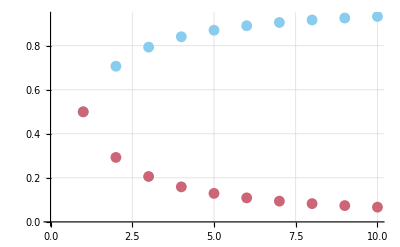

```mathematica
ListPlot[Evaluate@T@Table[{{n,2^(-1/n)},{n,1-2^(-1/n)}},{n,10}],GridLines->Auto]
```

```mathematica
{2^(-1/6),1-2^(-1/6)}//N
```

{0.890899,0.109101}

```mathematica
Solve[0.99^n==1/10,n]
```

{{n→229.105}}

```mathematica
(* error of maximum-likelihood *)
(13+1)/(13-1-6)//N
```

2.33333